```mathematica
(* Scrape data from HTML webpage saved *)
```

```mathematica
rawwebsite = Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\Ultimate Team - Atlanta Hustle 2017.html","Data"]
```

{{{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{A Olsen,9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{A Taylor,16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{Allan L,21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{Anonymous,1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{Archie,0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{Birdsong,0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{Boecking,6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{Bradham,4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{Bush,52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{C Olsen,23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{Caldwell,0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{Dylan,21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{Gainer,20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{Haskell,6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{Hunter,1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{Jaime,1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{JP Burns,18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{Justin M,2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{Kelvin,27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{Knowles,0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{Kyle S,18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{Lally,21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{Leonard,28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{M Smith,68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{Micah Jo,6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{Newman,1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{Parker,8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{Sears,20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{Sperling,1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{Staber,2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{Sun,16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{Thor,12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{Tree,4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{Trenton,11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{Vickroy,61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{AVERAGE,14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{TOTAL,3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}}},{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{A Olsen,9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{A Taylor,16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{Allan L,21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{Anonymous,1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{Archie,0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{Birdsong,0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{Boecking,6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{Bradham,4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{Bush,52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{C Olsen,23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{Caldwell,0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{Dylan,21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{Gainer,20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{Haskell,6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{Hunter,1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{Jaime,1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{JP Burns,18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{Justin M,2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{Kelvin,27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{Knowles,0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{Kyle S,18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{Lally,21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{Leonard,28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{M Smith,68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{Micah Jo,6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{Newman,1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{Parker,8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{Sears,20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{Sperling,1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{Staber,2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{Sun,16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{Thor,12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{Tree,4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{Trenton,11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{Vickroy,61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{AVERAGE,14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{TOTAL,3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}},{{Players,Games,Team},{Atlanta Hustle 2017,Opponents}}}

```mathematica
(* Get the data with levels *)
```

```mathematica
summary17 = rawwebsite[[3,2]];
```

```mathematica
(* Get the keys *)
```

```mathematica
keys=rawwebsite[[1,2,1]]
```

{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls}

```mathematica
(* Map the keys to the data, create dataset *)
```

```mathematica
team12017 = Dataset[Map[Association[Thread[Rule[keys,#]]]&,rawwebsite[[3,2,1;;Length[rawwebsite[[3,1]]]]]]]
```

Dataset[<>]

```mathematica
(* Create plots *)
```

```mathematica
(* O-line points played 2017 season AUDL Atlanta Hustle *)
```

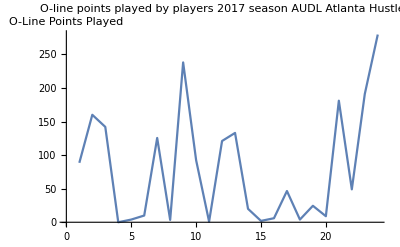

```mathematica
plot1 = ListLinePlot[team12017[1;;-3,6],Ticks->{None,Automatic},PlotLabel->"O-line points played by players 2017 season AUDL Atlanta Hustle",AxesLabel->{None,HoldForm["O-Line Points Played"]}]
```

```mathematica
(* All other teams 2017 AUDL season *)
rawwebsite2 = Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\Ultimate Team - Austin Sol 2017.html","Data"]
```

{{{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{Anonymous,-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{Bautis V,10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{Bennet M,34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{Best J,10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{Biersc M,22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{Bigley R,5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{Brooks C,0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{Cecil J,9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{Cunnin C,22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{Daftar K,2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{Davis A,9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{Deneco C,39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{Dial B,2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{Frohli J,2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{Graman B,-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{Hays M,29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{Henke K,7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{Kinney L,1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{Loskor J,16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{Matthi M,22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{Mock N,10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{Moore E,8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{Mosola L,6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{Naji S,3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{Orloff R,13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{Pollac E,14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{Purcel R,15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{Reinha J,-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{Richar D,27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{Sany N,8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{Schafe J,-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{Starke P,-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{Vargas C,1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{Walch A,28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{Walter M,30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{Wilder C,25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{AVERAGE,11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{TOTAL,3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}}},{{Players,Games,Team},{Sat, 7/01 5:55 vs. Nashville 27-21,Sun, 6/25 12:08 vs. Atlanta Hustle 26-25,Sat, 6/17 6:55 vs. Dallas 25-27,Sun, 6/04 3:47 vs. Atlanta Hustle 24-27,Sat, 6/03 5:55 vs. Nightwatch 28-24,Sat, 5/20 6:05 vs. Atlanta Hustle 27-28,Sun, 5/07 12:07 vs. Nashville Nightwatch 31-11,Sun, 4/30 12:58 vs. Jacksonville Cannons 22-30,Sat, 4/29 7:02 vs. Raleigh Flyers 23-28,Sat, 4/22 7:06 vs. Dallas Roughnecks 24-30,Sat, 4/08 7:11 vs. Raleigh Flyers 19-26,Sat, 4/01 6:57 vs. Dallas Roughnecks 17-21}},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{Anonymous,-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{Bautis V,10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{Bennet M,34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{Best J,10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{Biersc M,22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{Bigley R,5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{Brooks C,0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{Cecil J,9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{Cunnin C,22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{Daftar K,2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{Davis A,9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{Deneco C,39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{Dial B,2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{Frohli J,2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{Graman B,-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{Hays M,29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{Henke K,7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{Kinney L,1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{Loskor J,16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{Matthi M,22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{Mock N,10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{Moore E,8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{Mosola L,6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{Naji S,3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{Orloff R,13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{Pollac E,14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{Purcel R,15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{Reinha J,-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{Richar D,27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{Sany N,8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{Schafe J,-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{Starke P,-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{Vargas C,1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{Walch A,28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{Walter M,30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{Wilder C,25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{AVERAGE,11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{TOTAL,3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}},{{Players,Games,Team},{Austin Sol 2017,Opponents}}}

```mathematica
team22017 = Dataset[Map[Association[Thread[Rule[keys,#]]]&,rawwebsite2[[3,2,1;;Length[rawwebsite2[[3,1]]]]]]]
```

Dataset[<>]

```mathematica
Union[team12017,team22017]
```

Dataset[<>]

```mathematica
path = NotebookDirectory[];
```

```mathematica
<<"C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\dataset\\dataset.mx"
```

```mathematica
Get["dataset.mx",Path ->{"C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\dataset"}];
```

```mathematica
FilePrint["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\dataset\\dataset.mx"];
```

(*This is a Wolfram Language binary dump file. It can be loaded with Get.*).03à.06.0b"2016-06-11 18:07

```mathematica
NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\Ulti Analytics Summary Stats\

```mathematica
allNames={"C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\Ultimate Team - Atlanta Hustle 2017.html","C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\Ultimate Team - Austin Sol 2017.html"};
```

```mathematica
allData=Table[Import[allNames[[i]],"Data"],{i,1,Length[allNames]}];
```

```mathematica
%472
```

```mathematica
{{{{"Players","Games","Team"},{{"Player","+/-","Games played","Points played","Minutes played","O-line points played","+/- O-line","D-line points played","+/- D-line","Touches","Goals","Callahans","Assists","Throws","Throw aways","Stalled's","Passer Penalties (turnovers)","Callahaned's (other team scored)","Throw %","Catches","Drops","Catch %","Ds","Pulls","Avg Pull Hang Time","OB Pulls"},{{"A Olsen",9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{"A Taylor",16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{"Allan L",21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{"Anonymous",1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{"Archie",0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{"Birdsong",0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{"Boecking",6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{"Bradham",4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{"Bush",52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{"C Olsen",23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{"Caldwell",0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{"Dylan",21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{"Gainer",20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{"Haskell",6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{"Hunter",1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{"Jaime",1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{"JP Burns",18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{"Justin M",2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{"Kelvin",27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{"Knowles",0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{"Kyle S",18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{"Lally",21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{"Leonard",28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{"M Smith",68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{"Micah Jo",6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{"Newman",1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{"Parker",8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{"Sears",20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{"Sperling",1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{"Staber",2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{"Sun",16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{"Thor",12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{"Tree",4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{"Trenton",11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{"Vickroy",61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{"AVERAGE",14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{"TOTAL",3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}}},{"Players","Games","Team"},{{"Player","+/-","Games played","Points played","Minutes played","O-line points played","+/- O-line","D-line points played","+/- D-line","Touches","Goals","Callahans","Assists","Throws","Throw aways","Stalled's","Passer Penalties (turnovers)","Callahaned's (other team scored)","Throw %","Catches","Drops","Catch %","Ds","Pulls","Avg Pull Hang Time","OB Pulls"},{{"A Olsen",9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{"A Taylor",16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{"Allan L",21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{"Anonymous",1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{"Archie",0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{"Birdsong",0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{"Boecking",6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{"Bradham",4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{"Bush",52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{"C Olsen",23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{"Caldwell",0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{"Dylan",21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{"Gainer",20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{"Haskell",6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{"Hunter",1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{"Jaime",1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{"JP Burns",18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{"Justin M",2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{"Kelvin",27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{"Knowles",0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{"Kyle S",18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{"Lally",21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{"Leonard",28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{"M Smith",68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{"Micah Jo",6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{"Newman",1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{"Parker",8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{"Sears",20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{"Sperling",1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{"Staber",2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{"Sun",16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{"Thor",12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{"Tree",4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{"Trenton",11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{"Vickroy",61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{"AVERAGE",14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{"TOTAL",3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}},{{"Players","Games","Team"},{"Atlanta Hustle 2017","Opponents"}}},{{{"Players","Games","Team"},{{"Player","+/-","Games played","Points played","Minutes played","O-line points played","+/- O-line","D-line points played","+/- D-line","Touches","Goals","Callahans","Assists","Throws","Throw aways","Stalled's","Passer Penalties (turnovers)","Callahaned's (other team scored)","Throw %","Catches","Drops","Catch %","Ds","Pulls","Avg Pull Hang Time","OB Pulls"},{{"Anonymous",-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{"Bautis V",10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{"Bennet M",34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{"Best J",10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{"Biersc M",22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{"Bigley R",5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{"Brooks C",0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{"Cecil J",9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{"Cunnin C",22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{"Daftar K",2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{"Davis A",9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{"Deneco C",39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{"Dial B",2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{"Frohli J",2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{"Graman B",-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{"Hays M",29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{"Henke K",7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{"Kinney L",1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{"Loskor J",16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{"Matthi M",22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{"Mock N",10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{"Moore E",8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{"Mosola L",6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{"Naji S",3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{"Orloff R",13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{"Pollac E",14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{"Purcel R",15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{"Reinha J",-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{"Richar D",27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{"Sany N",8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{"Schafe J",-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{"Starke P",-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{"Vargas C",1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{"Walch A",28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{"Walter M",30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{"Wilder C",25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{"AVERAGE",11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{"TOTAL",3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}}},{{"Players","Games","Team"},{"Sat, 7/01 5:55 vs. Nashville 27-21","Sun, 6/25 12:08 vs. Atlanta Hustle 26-25","Sat, 6/17 6:55 vs. Dallas 25-27","Sun, 6/04 3:47 vs. Atlanta Hustle 24-27","Sat, 6/03 5:55 vs. Nightwatch 28-24","Sat, 5/20 6:05 vs. Atlanta Hustle 27-28","Sun, 5/07 12:07 vs. Nashville Nightwatch 31-11","Sun, 4/30 12:58 vs. Jacksonville Cannons 22-30","Sat, 4/29 7:02 vs. Raleigh Flyers 23-28","Sat, 4/22 7:06 vs. Dallas Roughnecks 24-30","Sat, 4/08 7:11 vs. Raleigh Flyers 19-26","Sat, 4/01 6:57 vs. Dallas Roughnecks 17-21"}},{{"Player","+/-","Games played","Points played","Minutes played","O-line points played","+/- O-line","D-line points played","+/- D-line","Touches","Goals","Callahans","Assists","Throws","Throw aways","Stalled's","Passer Penalties (turnovers)","Callahaned's (other team scored)","Throw %","Catches","Drops","Catch %","Ds","Pulls","Avg Pull Hang Time","OB Pulls"},{{"Anonymous",-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{"Bautis V",10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{"Bennet M",34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{"Best J",10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{"Biersc M",22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{"Bigley R",5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{"Brooks C",0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{"Cecil J",9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{"Cunnin C",22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{"Daftar K",2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{"Davis A",9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{"Deneco C",39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{"Dial B",2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{"Frohli J",2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{"Graman B",-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{"Hays M",29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{"Henke K",7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{"Kinney L",1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{"Loskor J",16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{"Matthi M",22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{"Mock N",10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{"Moore E",8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{"Mosola L",6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{"Naji S",3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{"Orloff R",13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{"Pollac E",14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{"Purcel R",15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{"Reinha J",-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{"Richar D",27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{"Sany N",8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{"Schafe J",-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{"Starke P",-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{"Vargas C",1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{"Walch A",28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{"Walter M",30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{"Wilder C",25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{"AVERAGE",11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{"TOTAL",3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}},{{"Players","Games","Team"},{"Austin Sol 2017","Opponents"}}}}
```

{{{{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{A Olsen,9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{A Taylor,16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{Allan L,21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{Anonymous,1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{Archie,0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{Birdsong,0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{Boecking,6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{Bradham,4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{Bush,52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{C Olsen,23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{Caldwell,0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{Dylan,21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{Gainer,20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{Haskell,6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{Hunter,1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{Jaime,1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{JP Burns,18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{Justin M,2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{Kelvin,27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{Knowles,0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{Kyle S,18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{Lally,21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{Leonard,28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{M Smith,68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{Micah Jo,6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{Newman,1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{Parker,8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{Sears,20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{Sperling,1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{Staber,2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{Sun,16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{Thor,12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{Tree,4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{Trenton,11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{Vickroy,61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{AVERAGE,14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{TOTAL,3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}}},{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{A Olsen,9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{A Taylor,16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{Allan L,21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{Anonymous,1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{Archie,0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{Birdsong,0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{Boecking,6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{Bradham,4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{Bush,52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{C Olsen,23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{Caldwell,0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{Dylan,21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{Gainer,20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{Haskell,6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{Hunter,1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{Jaime,1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{JP Burns,18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{Justin M,2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{Kelvin,27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{Knowles,0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{Kyle S,18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{Lally,21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{Leonard,28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{M Smith,68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{Micah Jo,6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{Newman,1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{Parker,8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{Sears,20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{Sperling,1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{Staber,2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{Sun,16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{Thor,12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{Tree,4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{Trenton,11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{Vickroy,61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{AVERAGE,14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{TOTAL,3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}},{{Players,Games,Team},{Atlanta Hustle 2017,Opponents}}},{{{Players,Games,Team},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{Anonymous,-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{Bautis V,10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{Bennet M,34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{Best J,10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{Biersc M,22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{Bigley R,5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{Brooks C,0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{Cecil J,9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{Cunnin C,22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{Daftar K,2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{Davis A,9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{Deneco C,39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{Dial B,2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{Frohli J,2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{Graman B,-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{Hays M,29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{Henke K,7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{Kinney L,1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{Loskor J,16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{Matthi M,22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{Mock N,10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{Moore E,8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{Mosola L,6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{Naji S,3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{Orloff R,13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{Pollac E,14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{Purcel R,15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{Reinha J,-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{Richar D,27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{Sany N,8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{Schafe J,-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{Starke P,-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{Vargas C,1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{Walch A,28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{Walter M,30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{Wilder C,25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{AVERAGE,11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{TOTAL,3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}}},{{Players,Games,Team},{Sat, 7/01 5:55 vs. Nashville 27-21,Sun, 6/25 12:08 vs. Atlanta Hustle 26-25,Sat, 6/17 6:55 vs. Dallas 25-27,Sun, 6/04 3:47 vs. Atlanta Hustle 24-27,Sat, 6/03 5:55 vs. Nightwatch 28-24,Sat, 5/20 6:05 vs. Atlanta Hustle 27-28,Sun, 5/07 12:07 vs. Nashville Nightwatch 31-11,Sun, 4/30 12:58 vs. Jacksonville Cannons 22-30,Sat, 4/29 7:02 vs. Raleigh Flyers 23-28,Sat, 4/22 7:06 vs. Dallas Roughnecks 24-30,Sat, 4/08 7:11 vs. Raleigh Flyers 19-26,Sat, 4/01 6:57 vs. Dallas Roughnecks 17-21}},{{Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},{{Anonymous,-3,0,0,0.,0,0,0,0,17,1,0,1,32,6,0,0,0,81,17,0,100,1,8,3.9,0},{Bautis V,10,10,122,137.4,10,3,112,-47,33,8,0,2,24,2,0,0,0,92,30,1,97,3,5,3.4,0},{Bennet M,34,10,212,236.3,170,89,42,-3,142,25,1,16,117,10,0,0,0,91,134,1,99,4,2,6.,0},{Best J,10,11,217,265.3,78,24,139,-70,241,6,0,11,235,19,0,0,0,92,186,0,100,12,26,5.8,3},{Biersc M,22,9,168,189.3,123,57,45,-23,104,16,0,17,87,11,0,0,0,87,93,3,97,3,1,6.6,0},{Bigley R,5,1,20.5,19.4,2.5,2,18,-7,9,0,0,2,9,0,0,0,0,100,5,0,100,3,0,0.,0},{Brooks C,0,1,14,19.2,7,2,7,-2,14,0,0,0,14,0,0,0,0,100,13,0,100,0,1,7.8,0},{Cecil J,9,6,90,102.9,11.5,0,78.5,-22,30,4,0,2,25,2,0,0,0,92,26,1,96,6,1,1.4,0},{Cunnin C,22,12,325.5,405.6,126.5,32,199,-92,267,9,0,37,255,34,0,0,0,87,210,5,98,15,143,5.9,15},{Daftar K,2,4,40,33.2,0,0,40,-17,4,2,0,0,2,1,0,0,0,50,4,0,100,1,0,0.,0},{Davis A,9,7,146.5,151.4,76,32,70.5,-31,146,10,0,14,134,17,1,0,0,87,104,0,100,3,9,5.2,0},{Deneco C,39,7,149,177.4,133,59,16,7,164,33,0,12,130,4,0,0,0,97,161,3,98,1,0,0.,0},{Dial B,2,7,73,74.,8,-4,65,-46,11,1,0,1,10,3,0,0,0,70,9,0,100,3,2,3.8,0},{Frohli J,2,4,53,65.5,4.5,0,48.5,-13,36,0,0,3,34,4,0,0,0,88,29,0,100,3,1,1.5,0},{Graman B,-2,2,26,41.6,14.5,0,11.5,-6,29,1,0,1,29,5,0,0,0,83,19,0,100,1,3,5.6,0},{Hays M,29,11,227.5,308.1,70.5,16,157,-75,85,19,0,8,65,7,0,0,0,89,76,1,99,10,0,0.,0},{Henke K,7,2,41.5,46.2,7,3,34.5,-14,10,5,0,2,5,0,0,0,0,100,10,0,100,0,1,6.6,0},{Kinney L,1,1,16,25.3,3,1,13,-2,16,0,0,1,16,0,0,0,0,100,14,0,100,0,0,0.,0},{Loskor J,16,5,110,145.5,75,40,35,1,221,2,0,19,217,10,1,0,0,95,187,2,99,8,0,0.,0},{Matthi M,22,9,197.5,272.,86.5,13,111,-53,137,12,0,13,124,12,0,0,0,90,123,1,99,10,1,6.3,1},{Mock N,10,8,115,108.6,36.5,8,78.5,-40,35,5,0,5,28,3,0,0,0,89,32,1,97,4,1,5.,0},{Moore E,8,4,50,65.9,4.5,0,45.5,-12,17,4,1,2,13,2,0,0,0,85,16,0,100,4,0,0.,0},{Mosola L,6,11,122.5,141.2,7.5,3,115,-69,28,5,0,3,23,2,0,0,0,91,25,3,89,3,0,0.,0},{Naji S,3,5,68,83.,12.5,4,55.5,-12,32,1,1,2,30,1,0,0,0,97,22,0,100,1,0,0.,1},{Orloff R,13,10,205,252.2,81.5,10,123.5,-67,134,10,0,5,123,7,0,0,0,94,98,0,100,5,9,4.8,0},{Pollac E,14,5,74.5,95.6,57,18,17.5,-2,69,10,0,6,59,3,0,0,0,95,68,2,97,3,0,0.,0},{Purcel R,15,9,214,234.8,161,80,53,-13,362,13,0,23,349,18,0,0,0,95,240,4,98,1,3,4.1,0},{Reinha J,-4,5,65,62.6,4,0,61,-48,22,0,0,0,21,4,0,0,0,81,18,2,90,2,45,6.5,5},{Richar D,27,9,210,258.,159,80,51,-14,360,25,0,20,333,15,2,0,0,95,304,3,99,2,8,5.3,0},{Sany N,8,6,105,102.3,71,45,34,-16,46,5,0,4,42,2,0,0,0,95,43,0,100,1,1,5.1,0},{Schafe J,-6,10,209.5,230.9,177,87,32.5,-6,301,5,0,24,296,33,2,0,0,88,251,2,99,2,6,5.1,0},{Starke P,-6,2,33,48.2,30,7,3,-1,82,0,0,5,81,11,0,0,0,86,60,1,98,1,0,0.,0},{Vargas C,1,4,63.5,89.5,48.5,22,15,-6,88,3,0,4,84,4,1,0,0,94,64,1,98,0,5,5.8,0},{Walch A,28,11,277.5,350.,202,96,75.5,-22,207,21,0,7,185,6,0,0,0,97,201,5,98,11,0,0.,0},{Walter M,30,10,204,267.3,89.5,32,114.5,-44,107,18,0,7,89,6,0,0,0,93,99,1,99,12,2,3.8,0},{Wilder C,25,6,146.5,175.6,97,29,49.5,-27,83,14,0,11,69,2,0,0,0,97,80,2,98,4,0,0.,0},{AVERAGE,11.3,6.5,122.6,62.4,24.7,60.2,-25.4,102.5,8.1,0.1,8.1,94.1,7.4,0.2,0.,0.,90.1,85.3,1.3,98.4,4.,7.9,0.7},{TOTAL,3689,293,3,290,3389,266,7,0,0,3071,45,143,284,25}}},{{Players,Games,Team},{Austin Sol 2017,Opponents}}}}

```mathematica
3
```

```mathematica
summary1 =  allData[[1,1,2,2]]
```

{{A Olsen,9,8,160,206.2,88.5,35,71.5,-39,94,12,0,6,82,10,0,0,0,88,90,1,99,2,0,0.,0},{A Taylor,16,9,198,223.,160,92,38,-9,146,8,0,15,136,4,1,0,0,96,141,3,98,1,0,0.,0},{Allan L,21,9,205,250.3,142,76,63,-27,240,10,0,24,228,17,0,0,0,93,170,2,99,6,45,7.2,2},{Anonymous,1,0,0,0.,0,0,0,0,0,0,0,0,4,0,0,0,0,100,0,0,0,1,19,2.2,0},{Archie,0,4,52,57.6,4,-3,48,-27,5,1,0,0,4,1,0,0,0,75,5,0,100,0,0,0.,0},{Birdsong,0,2,19,31.6,10,5,9,-9,8,0,0,0,8,0,0,0,0,100,8,0,100,0,0,0.,0},{Boecking,6,12,295,353.3,125.5,54,169.5,-87,294,2,0,14,289,22,0,0,1,92,209,3,99,15,34,5.8,1},{Bradham,4,8,102,110.2,3.5,-2,98.5,-68,9,3,0,1,6,0,0,0,0,100,8,1,89,1,0,0.,0},{Bush,52,12,279,338.6,238,125,41,-8,154,38,0,24,114,9,0,0,0,92,145,4,97,3,3,6.5,0},{C Olsen,23,10,204.5,265.4,92.5,39,112,-40,196,16,0,18,178,15,0,0,0,92,186,1,99,5,1,7.6,0},{Caldwell,0,2,22,26.9,1,0,21,-13,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0.,0},{Dylan,21,5,130,153.3,121,68,9,4,246,12,0,28,237,18,1,0,0,92,188,0,100,0,0,0.,0},{Gainer,20,9,182,208.1,133,68,49,-21,106,8,0,16,96,9,0,0,0,91,92,1,99,6,0,0.,0},{Haskell,6,3,46.5,62.6,20,11,26.5,-19,18,3,0,4,15,4,0,0,0,73,15,0,100,3,4,6.6,0},{Hunter,1,2,12,12.1,2,-1,10,-8,3,1,0,0,2,0,0,0,0,100,3,0,100,0,0,0.,0},{Jaime,1,7,81,70.4,6,1,75,-49,10,0,0,2,9,3,0,0,0,67,6,0,100,2,48,5.5,6},{JP Burns,18,13,250,337.7,46.5,8,203.5,-109,96,8,0,13,87,11,0,0,0,87,78,3,96,11,3,3.4,0},{Justin M,2,3,33,46.5,4,-2,29,-21,6,1,0,0,5,1,0,0,0,80,4,0,100,2,0,0.,0},{Kelvin,27,13,219,276.1,24.5,-8,194.5,-111,35,14,0,0,19,2,0,0,0,89,31,0,100,15,0,0.,0},{Knowles,0,5,59,68.4,9,3,50,-25,23,0,0,0,23,0,0,0,0,100,15,1,94,1,0,0.,0},{Kyle S,18,12,242.5,288.6,181,91,61.5,-17,267,8,0,15,257,9,0,0,0,96,198,0,100,4,29,6.3,1},{Lally,21,9,176.5,206.7,49,18,127.5,-59,95,13,0,8,81,9,0,0,0,89,89,1,99,10,35,5.5,2},{Leonard,28,9,205.5,258.5,191,85,14.5,8,349,14,0,24,336,10,0,0,0,97,250,1,100,1,0,0.,0},{M Smith,68,13,304,392.6,279.5,151,24.5,8,335,54,0,19,282,7,1,0,0,97,321,4,99,7,0,0.,0},{Micah Jo,6,2,35,31.9,32,22,3,-1,17,4,0,3,13,2,0,0,0,85,10,0,100,1,0,0.,0},{Newman,1,4,64.5,82.5,15,7,49.5,-27,25,4,0,0,21,5,0,0,0,76,16,1,94,3,1,0.,0},{Parker,8,7,148.5,188.3,52.5,7,96,-56,109,5,0,16,105,20,0,0,0,81,69,2,97,9,34,6.4,2},{Sears,20,10,163.5,229.4,22,0,141.5,-80,25,13,0,2,12,0,0,0,0,100,25,0,100,5,0,0.,0},{Sperling,1,3,40.5,52.8,20,7,20.5,-12,20,2,0,1,18,2,0,0,0,89,19,0,100,0,0,0.,0},{Staber,2,5,91.5,111.6,16,9,75.5,-41,37,2,0,3,34,4,0,0,0,88,24,0,100,1,1,0.,0},{Sun,16,12,198,248.2,42.5,16,155.5,-86,129,9,0,12,119,10,0,0,0,92,105,1,99,6,49,6.5,7},{Thor,12,9,118,135.5,24,2,94,-49,43,5,0,5,38,2,0,0,0,95,42,1,98,5,9,5.1,0},{Tree,4,4,50,45.7,5,-1,45,-25,12,1,0,2,11,2,0,0,0,82,8,0,100,3,2,7.1,0},{Trenton,11,10,173.5,225.5,33.5,12,140,-78,46,5,0,1,40,2,0,0,0,95,42,1,98,8,0,0.,0},{Vickroy,61,13,309.5,379.1,272.5,143,37,-3,287,41,0,41,244,29,1,0,0,88,264,2,99,11,2,5.9,0},{AVERAGE,14.4,7.4,139.1,70.5,32.5,68.7,-34.4,99.6,9.1,0.,9.1,90.1,6.9,0.1,0.,0.,87.3,82.2,1.,92.9,4.3,9.1,0.6},{TOTAL,3486,317,0,317,3154,240,4,0,1,2876,34,149,319,21}}

```mathematica
summary2 =  allData[[2,1,2,2]];
labelsum2={"name",summary2};
summary2[[1,2]]
stat=With[{t=summary2[[1]][[2]]},
For[i=2,i<Length[summary2]+1,i++,
Append[t,summary2[[i,2]]]
]]
```

-3

Append::normal: Nonatomic expression expected at position 1 in Append[-3,10].

Append::normal: Nonatomic expression expected at position 1 in Append[-3,34].

Append::normal: Nonatomic expression expected at position 1 in Append[-3,10].

General::stop: Further output of Append::normal will be suppressed during this calculation.